```mathematica
ϕex[x_,y_]= Sin[Pi x]Sinh[Pi(1-y)]/Sinh[Pi]+ 0.3 Sin[Pi y] Sinh[Pi x]/Sinh[Pi]
```

0.0259769 Sin[π y] Sinh[π x]+Csch[π] Sin[π x] Sinh[π (1-y)]

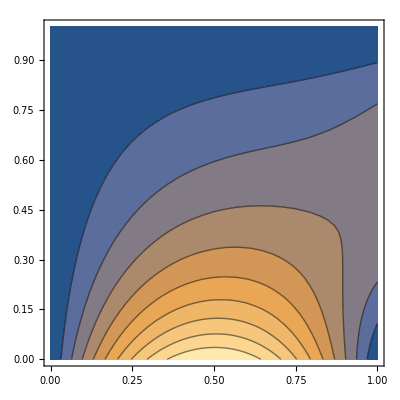

```mathematica
ContourPlot[ϕex[x,y],{x,0,1},{y,0,1}]
```

```mathematica
v[i_,j_,x_,y_]= x^i y^j x y (1-x)(1-y)
```

(1-x) x^(1+i) (1-y) y^(1+j)

```mathematica
u[x_,y_]= Sin[Pi x](1-y)+ x 0.3 Sin[Pi y];
```

```mathematica
ip[f_,g_]:= NIntegrate[ f g, {x,0,1},{y,0,1}]
```

```mathematica
op[f_]:= D[f,{x,2}]+D[f,{y,2}]
```

```mathematica
ρbar[x_,y_]= -op[u[x,y]]
```

0.+π^2 (1-y) Sin[π x]+2.96088 x Sin[π y]

```mathematica
ρ[i_,j_]:= ip[v[i,j,x,y],ρbar[x,y]]
```

```mathematica
ρ[1,2]//Timing
```

{0.03168,0.0160371}

```mathematica
L[k_,l_,i_,j_]:= ip[v[k,l,x,y], op[v[i,j,x,y]]]
```

```mathematica
L[1,2,3,4]
```

-0.000390126

```mathematica
eq[k_,l_]:=eq[k,l]= Sum[L[k,l,i,j]c[i,j],{i,0,5},{j,0,5}]==ρ[k,l]
```

```mathematica
eq[1,1]
```

-0.00555556 c[0,0]-0.00380952 c[0,1]-0.00265873 c[0,2]-0.00193122 c[0,3]-0.00145503 c[0,4]-0.00113035 c[0,5]-0.00380952 c[1,0]-0.00253968 c[1,1]-0.00174603 c[1,2]-0.00125472 c[1,3]-0.000937264 c[1,4]-0.000722875 c[1,5]-0.00265873 c[2,0]-0.00174603 c[2,1]-0.00119048 c[2,2]-0.00085034 c[2,3]-0.000632086 c[2,4]-0.000485467 c[2,5]-0.00193122 c[3,0]-0.00125472 c[3,1]-0.00085034 c[3,2]-0.000604686 c[3,3]-0.000447846 c[3,4]-0.000342885 c[3,5]-0.00145503 c[4,0]-0.000937264 c[4,1]-0.000632086 c[4,2]-0.000447846 c[4,3]-0.000330688 c[4,4]-0.000252525 c[4,5]-0.00113035 c[5,0]-0.000722875 c[5,1]-0.000485467 c[5,2]-0.000342885 c[5,3]-0.000252525 c[5,4]-0.0001924 c[5,5]==0.03077

```mathematica
Do[Print[k," ",l];Print[eq[k,l]],{k,0,5},{l,0,5}]
```

0 0

-0.0222222 c[0,0]-0.0111111 c[0,1]-0.00650794 c[0,2]-0.00420635 c[0,3]-0.00291005 c[0,4]-0.0021164 c[0,5]-0.0111111 c[1,0]-0.00555556 c[1,1]-0.00325397 c[1,2]-0.00210317 c[1,3]-0.00145503 c[1,4]-0.0010582 c[1,5]-0.00650794 c[2,0]-0.00325397 c[2,1]-0.00190476 c[2,2]-0.00123016 c[2,3]-0.00085034 c[2,4]-0.000617914 c[2,5]-0.00420635 c[3,0]-0.00210317 c[3,1]-0.00123016 c[3,2]-0.000793651 c[3,3]-0.000547997 c[3,4]-0.00039777 c[3,5]-0.00291005 c[4,0]-0.00145503 c[4,1]-0.00085034 c[4,2]-0.000547997 c[4,3]-0.000377929 c[4,4]-0.000273998 c[4,5]-0.0021164 c[5,0]-0.0010582 c[5,1]-0.000617914 c[5,2]-0.00039777 c[5,3]-0.000273998 c[5,4]-0.000198413 c[5,5]==0.137934

0 1

-0.0111111 c[0,0]-0.00761905 c[0,1]-0.00531746 c[0,2]-0.00386243 c[0,3]-0.00291005 c[0,4]-0.0022607 c[0,5]-0.00555556 c[1,0]-0.00380952 c[1,1]-0.00265873 c[1,2]-0.00193122 c[1,3]-0.00145503 c[1,4]-0.00113035 c[1,5]-0.00325397 c[2,0]-0.00222222 c[2,1]-0.00154762 c[2,2]-0.00112245 c[2,3]-0.000844671 c[2,4]-0.000655535 c[2,5]-0.00210317 c[3,0]-0.00142857 c[3,1]-0.000992064 c[3,2]-0.000718065 c[3,3]-0.000539494 c[3,4]-0.000418127 c[3,5]-0.00145503 c[4,0]-0.000982615 c[4,1]-0.000680272 c[4,2]-0.000491308 c[4,3]-0.000368481 c[4,4]-0.000285165 c[4,5]-0.0010582 c[5,0]-0.000710506 c[5,1]-0.000490363 c[5,2]-0.000353364 c[5,3]-0.00026455 c[5,4]-0.000204425 c[5,5]==0.0583568

0 2

-0.00650794 c[0,0]-0.00531746 c[0,1]-0.00417989 c[0,2]-0.00330688 c[0,3]-0.00265753 c[0,4]-0.00217172 c[0,5]-0.00325397 c[1,0]-0.00265873 c[1,1]-0.00208995 c[1,2]-0.00165344 c[1,3]-0.00132876 c[1,4]-0.00108586 c[1,5]-0.00190476 c[2,0]-0.00154762 c[2,1]-0.00121315 c[2,2]-0.00095805 c[2,3]-0.000768914 c[2,4]-0.000627706 c[2,5]-0.00123016 c[3,0]-0.000992063 c[3,1]-0.000774754 c[3,2]-0.000610355 c[3,3]-0.000488989 c[3,4]-0.000398629 c[3,5]-0.00085034 c[4,0]-0.000680272 c[4,1]-0.000529101 c[4,2]-0.000415722 c[4,3]-0.000332406 c[4,4]-0.000270563 c[4,5]-0.000617914 c[5,0]-0.000490363 c[5,1]-0.000379819 c[5,2]-0.000297619 c[5,3]-0.000237494 c[5,4]-0.000193001 c[5,5]==0.0302653

0 3

-0.00420635 c[0,0]-0.00386243 c[0,1]-0.00330688 c[0,2]-0.0027898 c[0,3]-0.0023569 c[0,4]-0.00200466 c[0,5]-0.00210317 c[1,0]-0.00193122 c[1,1]-0.00165344 c[1,2]-0.0013949 c[1,3]-0.00117845 c[1,4]-0.00100233 c[1,5]-0.00123016 c[2,0]-0.00112245 c[2,1]-0.00095805 c[2,2]-0.000806707 c[2,3]-0.000680616 c[2,4]-0.000578311 c[2,5]-0.000793651 c[3,0]-0.000718065 c[3,1]-0.000610355 c[3,2]-0.000512609 c[3,3]-0.000431698 c[3,4]-0.0003663 c[3,5]-0.000547997 c[4,0]-0.000491308 c[4,1]-0.000415722 c[4,2]-0.000348153 c[4,3]-0.000292609 c[4,4]-0.0002479 c[4,5]-0.00039777 c[5,0]-0.000353364 c[5,1]-0.000297619 c[5,2]-0.000248517 c[5,3]-0.000208434 c[5,4]-0.000176305 c[5,5]==0.0177353

0 4

-0.00291005 c[0,0]-0.00291005 c[0,1]-0.00265753 c[0,2]-0.0023569 c[0,3]-0.002072 c[0,4]-0.0018204 c[0,5]-0.00145503 c[1,0]-0.00145503 c[1,1]-0.00132876 c[1,2]-0.00117845 c[1,3]-0.001036 c[1,4]-0.000910201 c[1,5]-0.00085034 c[2,0]-0.000844671 c[2,1]-0.000768914 c[2,2]-0.000680616 c[2,3]-0.000597551 c[2,4]-0.000524476 c[2,5]-0.000547997 c[3,0]-0.000539494 c[3,1]-0.000488989 c[3,2]-0.000431698 c[3,3]-0.000378325 c[3,4]-0.000331613 c[3,5]-0.000377929 c[4,0]-0.000368481 c[4,1]-0.000332406 c[4,2]-0.000292609 c[4,3]-0.000255917 c[4,4]-0.000223982 c[4,5]-0.000273998 c[5,0]-0.00026455 c[5,1]-0.000237494 c[5,2]-0.000208434 c[5,3]-0.000181917 c[5,4]-0.000158968 c[5,5]==0.0112866

0 5

-0.0021164 c[0,0]-0.0022607 c[0,1]-0.00217172 c[0,2]-0.00200466 c[0,3]-0.0018204 c[0,4]-0.0016428 c[0,5]-0.0010582 c[1,0]-0.00113035 c[1,1]-0.00108586 c[1,2]-0.00100233 c[1,3]-0.000910201 c[1,4]-0.000821401 c[1,5]-0.000617914 c[2,0]-0.000655535 c[2,1]-0.000627706 c[2,2]-0.000578311 c[2,3]-0.000524476 c[2,4]-0.00047286 c[2,5]-0.00039777 c[3,0]-0.000418127 c[3,1]-0.000398629 c[3,2]-0.0003663 c[3,3]-0.000331613 c[3,4]-0.00029859 c[3,5]-0.000273998 c[4,0]-0.000285165 c[4,1]-0.000270563 c[4,2]-0.0002479 c[4,3]-0.000223982 c[4,4]-0.000201386 c[4,5]-0.000198413 c[5,0]-0.000204425 c[5,1]-0.000193001 c[5,2]-0.000176305 c[5,3]-0.000158968 c[5,4]-0.000142714 c[5,5]==0.00762582

1 0

-0.0111111 c[0,0]-0.00555556 c[0,1]-0.00325397 c[0,2]-0.00210317 c[0,3]-0.00145503 c[0,4]-0.0010582 c[0,5]-0.00761905 c[1,0]-0.00380952 c[1,1]-0.00222222 c[1,2]-0.00142857 c[1,3]-0.000982615 c[1,4]-0.000710506 c[1,5]-0.00531746 c[2,0]-0.00265873 c[2,1]-0.00154762 c[2,2]-0.000992064 c[2,3]-0.000680272 c[2,4]-0.000490363 c[2,5]-0.00386243 c[3,0]-0.00193122 c[3,1]-0.00112245 c[3,2]-0.000718065 c[3,3]-0.000491308 c[3,4]-0.000353364 c[3,5]-0.00291005 c[4,0]-0.00145503 c[4,1]-0.000844671 c[4,2]-0.000539494 c[4,3]-0.000368481 c[4,4]-0.00026455 c[4,5]-0.0022607 c[5,0]-0.00113035 c[5,1]-0.000655535 c[5,2]-0.000418127 c[5,3]-0.000285165 c[5,4]-0.000204425 c[5,5]==0.0721502

1 1

-0.00555556 c[0,0]-0.00380952 c[0,1]-0.00265873 c[0,2]-0.00193122 c[0,3]-0.00145503 c[0,4]-0.00113035 c[0,5]-0.00380952 c[1,0]-0.00253968 c[1,1]-0.00174603 c[1,2]-0.00125472 c[1,3]-0.000937264 c[1,4]-0.000722875 c[1,5]-0.00265873 c[2,0]-0.00174603 c[2,1]-0.00119048 c[2,2]-0.00085034 c[2,3]-0.000632086 c[2,4]-0.000485467 c[2,5]-0.00193122 c[3,0]-0.00125472 c[3,1]-0.00085034 c[3,2]-0.000604686 c[3,3]-0.000447846 c[3,4]-0.000342885 c[3,5]-0.00145503 c[4,0]-0.000937264 c[4,1]-0.000632086 c[4,2]-0.000447846 c[4,3]-0.000330688 c[4,4]-0.000252525 c[4,5]-0.00113035 c[5,0]-0.000722875 c[5,1]-0.000485467 c[5,2]-0.000342885 c[5,3]-0.000252525 c[5,4]-0.0001924 c[5,5]==0.03077

1 2

-0.00325397 c[0,0]-0.00265873 c[0,1]-0.00208995 c[0,2]-0.00165344 c[0,3]-0.00132876 c[0,4]-0.00108586 c[0,5]-0.00222222 c[1,0]-0.00174603 c[1,1]-0.00134543 c[1,2]-0.00105064 c[1,3]-0.000836254 c[1,4]-0.000678211 c[1,5]-0.00154762 c[2,0]-0.00119048 c[2,1]-0.000907029 c[2,2]-0.000702948 c[2,3]-0.000556329 c[2,4]-0.000449134 c[2,5]-0.00112245 c[3,0]-0.00085034 c[3,1]-0.000642479 c[3,2]-0.000495087 c[3,3]-0.000390126 c[3,4]-0.000313853 c[3,5]-0.000844671 c[4,0]-0.000632086 c[4,1]-0.000474301 c[4,2]-0.000363757 c[4,3]-0.000285594 c[4,4]-0.000229076 c[4,5]-0.000655535 c[5,0]-0.000485467 c[5,1]-0.000362125 c[5,2]-0.000276575 c[5,3]-0.00021645 c[5,4]-0.00017316 c[5,5]==0.0160371

1 3

-0.00210317 c[0,0]-0.00193122 c[0,1]-0.00165344 c[0,2]-0.0013949 c[0,3]-0.00117845 c[0,4]-0.00100233 c[0,5]-0.00142857 c[1,0]-0.00125472 c[1,1]-0.00105064 c[1,2]-0.000874047 c[1,3]-0.000731121 c[1,4]-0.000617161 c[1,5]-0.000992063 c[2,0]-0.00085034 c[2,1]-0.000702948 c[2,2]-0.000579949 c[2,3]-0.000482203 c[2,4]-0.00040515 c[2,5]-0.000718065 c[3,0]-0.000604686 c[3,1]-0.000495087 c[3,2]-0.000405873 c[3,3]-0.000335899 c[3,4]-0.0002812 c[3,5]-0.000539494 c[4,0]-0.000447846 c[4,1]-0.000363757 c[4,2]-0.000296617 c[4,3]-0.000244509 c[4,4]-0.000204055 c[4,5]-0.000418127 c[5,0]-0.000342885 c[5,1]-0.000276575 c[5,2]-0.000224467 c[5,3]-0.000184384 c[5,4]-0.000153449 c[5,5]==0.00942857

1 4

-0.00145503 c[0,0]-0.00145503 c[0,1]-0.00132876 c[0,2]-0.00117845 c[0,3]-0.001036 c[0,4]-0.000910201 c[0,5]-0.000982615 c[1,0]-0.000937264 c[1,1]-0.000836254 c[1,2]-0.000731121 c[1,3]-0.000636401 c[1,4]-0.000555001 c[1,5]-0.000680272 c[2,0]-0.000632086 c[2,1]-0.000556329 c[2,2]-0.000482203 c[2,3]-0.000417175 c[2,4]-0.000362138 c[2,5]-0.000491308 c[3,0]-0.000447846 c[3,1]-0.000390126 c[3,2]-0.000335899 c[3,3]-0.000289217 c[3,4]-0.000250147 c[3,5]-0.000368481 c[4,0]-0.000330688 c[4,1]-0.000285594 c[4,2]-0.000244509 c[4,3]-0.000209667 c[4,4]-0.000180772 c[4,5]-0.000285165 c[5,0]-0.000252525 c[5,1]-0.00021645 c[5,2]-0.000184384 c[5,3]-0.00015753 c[5,4]-0.000135435 c[5,5]==0.00601406

1 5

-0.0010582 c[0,0]-0.00113035 c[0,1]-0.00108586 c[0,2]-0.00100233 c[0,3]-0.000910201 c[0,4]-0.000821401 c[0,5]-0.000710506 c[1,0]-0.000722875 c[1,1]-0.000678211 c[1,2]-0.000617161 c[1,3]-0.000555001 c[1,4]-0.00049728 c[1,5]-0.000490363 c[2,0]-0.000485467 c[2,1]-0.000449134 c[2,2]-0.00040515 c[2,3]-0.000362138 c[2,4]-0.00032301 c[2,5]-0.000353364 c[3,0]-0.000342885 c[3,1]-0.000313853 c[3,2]-0.0002812 c[3,3]-0.000250147 c[3,4]-0.000222317 c[3,5]-0.00026455 c[4,0]-0.000252525 c[4,1]-0.000229076 c[4,2]-0.000204055 c[4,3]-0.000180772 c[4,4]-0.000160157 c[4,5]-0.000204425 c[5,0]-0.0001924 c[5,1]-0.00017316 c[5,2]-0.000153449 c[5,3]-0.000135435 c[5,4]-0.000119649 c[5,5]==0.00407024

2 0

-0.00650794 c[0,0]-0.00325397 c[0,1]-0.00190476 c[0,2]-0.00123016 c[0,3]-0.00085034 c[0,4]-0.000617914 c[0,5]-0.00531746 c[1,0]-0.00265873 c[1,1]-0.00154762 c[1,2]-0.000992063 c[1,3]-0.000680272 c[1,4]-0.000490363 c[1,5]-0.00417989 c[2,0]-0.00208995 c[2,1]-0.00121315 c[2,2]-0.000774754 c[2,3]-0.000529101 c[2,4]-0.000379819 c[2,5]-0.00330688 c[3,0]-0.00165344 c[3,1]-0.00095805 c[3,2]-0.000610355 c[3,3]-0.000415722 c[3,4]-0.000297619 c[3,5]-0.00265753 c[4,0]-0.00132876 c[4,1]-0.000768914 c[4,2]-0.000488989 c[4,3]-0.000332406 c[4,4]-0.000237494 c[4,5]-0.00217172 c[5,0]-0.00108586 c[5,1]-0.000627706 c[5,2]-0.000398629 c[5,3]-0.000270563 c[5,4]-0.000193001 c[5,5]==0.0428812

2 1

-0.00325397 c[0,0]-0.00222222 c[0,1]-0.00154762 c[0,2]-0.00112245 c[0,3]-0.000844671 c[0,4]-0.000655535 c[0,5]-0.00265873 c[1,0]-0.00174603 c[1,1]-0.00119048 c[1,2]-0.00085034 c[1,3]-0.000632086 c[1,4]-0.000485467 c[1,5]-0.00208995 c[2,0]-0.00134543 c[2,1]-0.000907029 c[2,2]-0.000642479 c[2,3]-0.000474301 c[2,4]-0.000362125 c[2,5]-0.00165344 c[3,0]-0.00105064 c[3,1]-0.000702948 c[3,2]-0.000495087 c[3,3]-0.000363757 c[3,4]-0.000276575 c[3,5]-0.00132876 c[4,0]-0.000836254 c[4,1]-0.000556329 c[4,2]-0.000390126 c[4,3]-0.000285594 c[4,4]-0.00021645 c[4,5]-0.00108586 c[5,0]-0.000678211 c[5,1]-0.000449134 c[5,2]-0.000313853 c[5,3]-0.000229076 c[5,4]-0.00017316 c[5,5]==0.0184257

2 2

-0.00190476 c[0,0]-0.00154762 c[0,1]-0.00121315 c[0,2]-0.00095805 c[0,3]-0.000768914 c[0,4]-0.000627706 c[0,5]-0.00154762 c[1,0]-0.00119048 c[1,1]-0.000907029 c[1,2]-0.000702948 c[1,3]-0.000556329 c[1,4]-0.000449134 c[1,5]-0.00121315 c[2,0]-0.000907029 c[2,1]-0.000680272 c[2,2]-0.000521542 c[2,3]-0.000409366 c[2,4]-0.000328283 c[2,5]-0.00095805 c[3,0]-0.000702948 c[3,1]-0.000521542 c[3,2]-0.000396825 c[3,3]-0.000309644 c[3,4]-0.000247114 c[3,5]-0.000768914 c[4,0]-0.000556329 c[4,1]-0.000409366 c[4,2]-0.000309644 c[4,3]-0.0002405 c[4,4]-0.000191198 c[4,5]-0.000627706 c[5,0]-0.000449134 c[5,1]-0.000328283 c[5,2]-0.000247114 c[5,3]-0.000191198 c[5,4]-0.000151515 c[5,5]==0.00964762

2 3

-0.00123016 c[0,0]-0.00112245 c[0,1]-0.00095805 c[0,2]-0.000806707 c[0,3]-0.000680616 c[0,4]-0.000578311 c[0,5]-0.000992063 c[1,0]-0.00085034 c[1,1]-0.000702948 c[1,2]-0.000579949 c[1,3]-0.000482203 c[1,4]-0.00040515 c[1,5]-0.000774754 c[2,0]-0.000642479 c[2,1]-0.000521542 c[2,2]-0.000425113 c[2,3]-0.000350329 c[2,4]-0.0002923 c[2,5]-0.000610355 c[3,0]-0.000495087 c[3,1]-0.000396825 c[3,2]-0.000320667 c[3,3]-0.000262546 c[3,4]-0.00021793 c[3,5]-0.000488989 c[4,0]-0.000390126 c[4,1]-0.000309644 c[4,2]-0.000248517 c[4,3]-0.000202421 c[4,4]-0.000167324 c[4,5]-0.000398629 c[5,0]-0.000313853 c[5,1]-0.000247114 c[5,2]-0.00019721 c[5,3]-0.000159933 c[5,4]-0.000131737 c[5,5]==0.00568926

2 4

-0.00085034 c[0,0]-0.000844671 c[0,1]-0.000768914 c[0,2]-0.000680616 c[0,3]-0.000597551 c[0,4]-0.000524476 c[0,5]-0.000680272 c[1,0]-0.000632086 c[1,1]-0.000556329 c[1,2]-0.000482203 c[1,3]-0.000417175 c[1,4]-0.000362138 c[1,5]-0.000529101 c[2,0]-0.000474301 c[2,1]-0.000409366 c[2,2]-0.000350329 c[2,3]-0.000300317 c[2,4]-0.000258868 c[2,5]-0.000415722 c[3,0]-0.000363757 c[3,1]-0.000309644 c[3,2]-0.000262546 c[3,3]-0.000223542 c[3,4]-0.000191673 c[3,5]-0.000332406 c[4,0]-0.000285594 c[4,1]-0.0002405 c[4,2]-0.000202421 c[4,3]-0.000171405 c[4,4]-0.000146336 c[4,5]-0.000270563 c[5,0]-0.000229076 c[5,1]-0.000191198 c[5,2]-0.000159933 c[5,3]-0.000134798 c[5,4]-0.000114658 c[5,5]==0.00363659

2 5

-0.000617914 c[0,0]-0.000655535 c[0,1]-0.000627706 c[0,2]-0.000578311 c[0,3]-0.000524476 c[0,4]-0.00047286 c[0,5]-0.000490363 c[1,0]-0.000485467 c[1,1]-0.000449134 c[1,2]-0.00040515 c[1,3]-0.000362138 c[1,4]-0.00032301 c[1,5]-0.000379819 c[2,0]-0.000362125 c[2,1]-0.000328283 c[2,2]-0.0002923 c[2,3]-0.000258868 c[2,4]-0.000229295 c[2,5]-0.000297619 c[3,0]-0.000276575 c[3,1]-0.000247114 c[3,2]-0.00021793 c[3,3]-0.000191673 c[3,4]-0.000168879 c[3,5]-0.000237494 c[4,0]-0.00021645 c[4,1]-0.000191198 c[4,2]-0.000167324 c[4,3]-0.000146336 c[4,4]-0.000128371 c[4,5]-0.000193001 c[5,0]-0.00017316 c[5,1]-0.000151515 c[5,2]-0.000131737 c[5,3]-0.000114658 c[5,4]-0.000100203 c[5,5]==0.00246497

3 0

-0.00420635 c[0,0]-0.00210317 c[0,1]-0.00123016 c[0,2]-0.000793651 c[0,3]-0.000547997 c[0,4]-0.00039777 c[0,5]-0.00386243 c[1,0]-0.00193122 c[1,1]-0.00112245 c[1,2]-0.000718065 c[1,3]-0.000491308 c[1,4]-0.000353364 c[1,5]-0.00330688 c[2,0]-0.00165344 c[2,1]-0.00095805 c[2,2]-0.000610355 c[2,3]-0.000415722 c[2,4]-0.000297619 c[2,5]-0.0027898 c[3,0]-0.0013949 c[3,1]-0.000806707 c[3,2]-0.000512609 c[3,3]-0.000348153 c[3,4]-0.000248517 c[3,5]-0.0023569 c[4,0]-0.00117845 c[4,1]-0.000680616 c[4,2]-0.000431698 c[4,3]-0.000292609 c[4,4]-0.000208434 c[4,5]-0.00200466 c[5,0]-0.00100233 c[5,1]-0.000578311 c[5,2]-0.0003663 c[5,3]-0.0002479 c[5,4]-0.000176305 c[5,5]==0.027792

3 1

-0.00210317 c[0,0]-0.00142857 c[0,1]-0.000992063 c[0,2]-0.000718065 c[0,3]-0.000539494 c[0,4]-0.000418127 c[0,5]-0.00193122 c[1,0]-0.00125472 c[1,1]-0.00085034 c[1,2]-0.000604686 c[1,3]-0.000447846 c[1,4]-0.000342885 c[1,5]-0.00165344 c[2,0]-0.00105064 c[2,1]-0.000702948 c[2,2]-0.000495087 c[2,3]-0.000363757 c[2,4]-0.000276575 c[2,5]-0.0013949 c[3,0]-0.000874047 c[3,1]-0.000579949 c[3,2]-0.000405873 c[3,3]-0.000296617 c[3,4]-0.000224467 c[3,5]-0.00117845 c[4,0]-0.000731121 c[4,1]-0.000482203 c[4,2]-0.000335899 c[4,3]-0.000244509 c[4,4]-0.000184384 c[4,5]-0.00100233 c[5,0]-0.000617161 c[5,1]-0.00040515 c[5,2]-0.0002812 c[5,3]-0.000204055 c[5,4]-0.000153449 c[5,5]==0.0120262

3 2

-0.00123016 c[0,0]-0.000992063 c[0,1]-0.000774754 c[0,2]-0.000610355 c[0,3]-0.000488989 c[0,4]-0.000398629 c[0,5]-0.00112245 c[1,0]-0.00085034 c[1,1]-0.000642479 c[1,2]-0.000495087 c[1,3]-0.000390126 c[1,4]-0.000313853 c[1,5]-0.00095805 c[2,0]-0.000702948 c[2,1]-0.000521542 c[2,2]-0.000396825 c[2,3]-0.000309644 c[2,4]-0.000247114 c[2,5]-0.000806707 c[3,0]-0.000579949 c[3,1]-0.000425113 c[3,2]-0.000320667 c[3,3]-0.000248517 c[3,4]-0.00019721 c[3,5]-0.000680616 c[4,0]-0.000482203 c[4,1]-0.000350329 c[4,2]-0.000262546 c[4,3]-0.000202421 c[4,4]-0.000159933 c[4,5]-0.000578311 c[5,0]-0.00040515 c[5,1]-0.0002923 c[5,2]-0.00021793 c[5,3]-0.000167324 c[5,4]-0.000131737 c[5,5]==0.00632366

3 3

-0.000793651 c[0,0]-0.000718065 c[0,1]-0.000610355 c[0,2]-0.000512609 c[0,3]-0.000431698 c[0,4]-0.0003663 c[0,5]-0.000718065 c[1,0]-0.000604686 c[1,1]-0.000495087 c[1,2]-0.000405873 c[1,3]-0.000335899 c[1,4]-0.0002812 c[1,5]-0.000610355 c[2,0]-0.000495087 c[2,1]-0.000396826 c[2,2]-0.000320667 c[2,3]-0.000262546 c[2,4]-0.00021793 c[2,5]-0.000512609 c[3,0]-0.000405873 c[3,1]-0.000320667 c[3,2]-0.000256534 c[3,3]-0.000208434 c[3,4]-0.000171949 c[3,5]-0.000431698 c[4,0]-0.000335899 c[4,1]-0.000262546 c[4,2]-0.000208434 c[4,3]-0.00016835 c[4,4]-0.000138212 c[4,5]-0.0003663 c[5,0]-0.0002812 c[5,1]-0.00021793 c[5,2]-0.000171949 c[5,3]-0.000138212 c[5,4]-0.000113018 c[5,5]==0.00373948

3 4

-0.000547997 c[0,0]-0.000539494 c[0,1]-0.000488989 c[0,2]-0.000431698 c[0,3]-0.000378325 c[0,4]-0.000331613 c[0,5]-0.000491308 c[1,0]-0.000447846 c[1,1]-0.000390126 c[1,2]-0.000335899 c[1,3]-0.000289217 c[1,4]-0.000250147 c[1,5]-0.000415722 c[2,0]-0.000363757 c[2,1]-0.000309644 c[2,2]-0.000262546 c[2,3]-0.000223542 c[2,4]-0.000191673 c[2,5]-0.000348153 c[3,0]-0.000296617 c[3,1]-0.000248517 c[3,2]-0.000208434 c[3,3]-0.00017603 c[3,4]-0.00014997 c[3,5]-0.000292609 c[4,0]-0.000244509 c[4,1]-0.000202421 c[4,2]-0.00016835 c[4,3]-0.000141273 c[4,4]-0.000119746 c[4,5]-0.0002479 c[5,0]-0.000204055 c[5,1]-0.000167324 c[5,2]-0.000138212 c[5,3]-0.000115373 c[5,4]-0.0000973774 c[5,5]==0.00239489

3 5

-0.00039777 c[0,0]-0.000418127 c[0,1]-0.000398629 c[0,2]-0.0003663 c[0,3]-0.000331613 c[0,4]-0.00029859 c[0,5]-0.000353364 c[1,0]-0.000342885 c[1,1]-0.000313853 c[1,2]-0.0002812 c[1,3]-0.000250147 c[1,4]-0.000222317 c[1,5]-0.000297619 c[2,0]-0.000276575 c[2,1]-0.000247114 c[2,2]-0.00021793 c[2,3]-0.000191673 c[2,4]-0.000168879 c[2,5]-0.000248517 c[3,0]-0.000224467 c[3,1]-0.00019721 c[3,2]-0.000171949 c[3,3]-0.00014997 c[3,4]-0.000131278 c[3,5]-0.000208434 c[4,0]-0.000184384 c[4,1]-0.000159933 c[4,2]-0.000138212 c[4,3]-0.000119746 c[4,4]-0.000104273 c[4,5]-0.000176305 c[5,0]-0.000153449 c[5,1]-0.000131737 c[5,2]-0.000113018 c[5,3]-0.0000973774 c[5,4]-0.0000844222 c[5,5]==0.00162557

4 0

-0.00291005 c[0,0]-0.00145503 c[0,1]-0.00085034 c[0,2]-0.000547997 c[0,3]-0.000377929 c[0,4]-0.000273998 c[0,5]-0.00291005 c[1,0]-0.00145503 c[1,1]-0.000844671 c[1,2]-0.000539494 c[1,3]-0.000368481 c[1,4]-0.00026455 c[1,5]-0.00265753 c[2,0]-0.00132876 c[2,1]-0.000768914 c[2,2]-0.000488989 c[2,3]-0.000332406 c[2,4]-0.000237494 c[2,5]-0.0023569 c[3,0]-0.00117845 c[3,1]-0.000680616 c[3,2]-0.000431698 c[3,3]-0.000292609 c[3,4]-0.000208434 c[3,5]-0.002072 c[4,0]-0.001036 c[4,1]-0.000597551 c[4,2]-0.000378325 c[4,3]-0.000255917 c[4,4]-0.000181917 c[4,5]-0.0018204 c[5,0]-0.000910201 c[5,1]-0.000524476 c[5,2]-0.000331613 c[5,3]-0.000223982 c[5,4]-0.000158968 c[5,5]==0.0191801

4 1

-0.00145503 c[0,0]-0.000982615 c[0,1]-0.000680272 c[0,2]-0.000491308 c[0,3]-0.000368481 c[0,4]-0.000285165 c[0,5]-0.00145503 c[1,0]-0.000937264 c[1,1]-0.000632086 c[1,2]-0.000447846 c[1,3]-0.000330688 c[1,4]-0.000252525 c[1,5]-0.00132876 c[2,0]-0.000836254 c[2,1]-0.000556329 c[2,2]-0.000390126 c[2,3]-0.000285594 c[2,4]-0.00021645 c[2,5]-0.00117845 c[3,0]-0.000731121 c[3,1]-0.000482203 c[3,2]-0.000335899 c[3,3]-0.000244509 c[3,4]-0.000184384 c[3,5]-0.001036 c[4,0]-0.000636401 c[4,1]-0.000417175 c[4,2]-0.000289217 c[4,3]-0.000209667 c[4,4]-0.00015753 c[4,5]-0.000910201 c[5,0]-0.000555001 c[5,1]-0.000362138 c[5,2]-0.000250147 c[5,3]-0.000180772 c[5,4]-0.000135435 c[5,5]==0.00835414

4 2

-0.00085034 c[0,0]-0.000680272 c[0,1]-0.000529101 c[0,2]-0.000415722 c[0,3]-0.000332406 c[0,4]-0.000270563 c[0,5]-0.000844671 c[1,0]-0.000632086 c[1,1]-0.000474301 c[1,2]-0.000363757 c[1,3]-0.000285594 c[1,4]-0.000229076 c[1,5]-0.000768914 c[2,0]-0.000556329 c[2,1]-0.000409366 c[2,2]-0.000309644 c[2,3]-0.0002405 c[2,4]-0.000191198 c[2,5]-0.000680616 c[3,0]-0.000482203 c[3,1]-0.000350329 c[3,2]-0.000262546 c[3,3]-0.000202421 c[3,4]-0.000159933 c[3,5]-0.000597551 c[4,0]-0.000417175 c[4,1]-0.000300317 c[4,2]-0.000223542 c[4,3]-0.000171405 c[4,4]-0.000134798 c[4,5]-0.000524476 c[5,0]-0.000362138 c[5,1]-0.000258868 c[5,2]-0.000191673 c[5,3]-0.000146336 c[5,4]-0.000114658 c[5,5]==0.00440997

4 3

-0.000547997 c[0,0]-0.000491308 c[0,1]-0.000415722 c[0,2]-0.000348153 c[0,3]-0.000292609 c[0,4]-0.0002479 c[0,5]-0.000539494 c[1,0]-0.000447846 c[1,1]-0.000363757 c[1,2]-0.000296617 c[1,3]-0.000244509 c[1,4]-0.000204055 c[1,5]-0.000488989 c[2,0]-0.000390126 c[2,1]-0.000309644 c[2,2]-0.000248517 c[2,3]-0.000202421 c[2,4]-0.000167324 c[2,5]-0.000431698 c[3,0]-0.000335899 c[3,1]-0.000262546 c[3,2]-0.000208434 c[3,3]-0.00016835 c[3,4]-0.000138212 c[3,5]-0.000378325 c[4,0]-0.000289217 c[4,1]-0.000223542 c[4,2]-0.00017603 c[4,3]-0.000141273 c[4,4]-0.000115373 c[4,5]-0.000331613 c[5,0]-0.000250147 c[5,1]-0.000191673 c[5,2]-0.00014997 c[5,3]-0.000119746 c[5,4]-0.0000973774 c[5,5]==0.00261445

4 4

-0.000377929 c[0,0]-0.000368481 c[0,1]-0.000332406 c[0,2]-0.000292609 c[0,3]-0.000255917 c[0,4]-0.000223982 c[0,5]-0.000368481 c[1,0]-0.000330688 c[1,1]-0.000285594 c[1,2]-0.000244509 c[1,3]-0.000209667 c[1,4]-0.000180772 c[1,5]-0.000332406 c[2,0]-0.000285594 c[2,1]-0.0002405 c[2,2]-0.000202421 c[2,3]-0.000171405 c[2,4]-0.000146336 c[2,5]-0.000292609 c[3,0]-0.000244509 c[3,1]-0.000202421 c[3,2]-0.00016835 c[3,3]-0.000141273 c[3,4]-0.000119746 c[3,5]-0.000255917 c[4,0]-0.000209667 c[4,1]-0.000171405 c[4,2]-0.000141273 c[4,3]-0.000117727 c[4,4]-0.0000992274 c[4,5]-0.000223982 c[5,0]-0.000180772 c[5,1]-0.000146336 c[5,2]-0.000119746 c[5,3]-0.0000992274 c[5,4]-0.0000832501 c[5,5]==0.00167732

4 5

-0.000273998 c[0,0]-0.000285165 c[0,1]-0.000270563 c[0,2]-0.0002479 c[0,3]-0.000223982 c[0,4]-0.000201386 c[0,5]-0.00026455 c[1,0]-0.000252525 c[1,1]-0.000229076 c[1,2]-0.000204055 c[1,3]-0.000180772 c[1,4]-0.000160157 c[1,5]-0.000237494 c[2,0]-0.00021645 c[2,1]-0.000191198 c[2,2]-0.000167324 c[2,3]-0.000146336 c[2,4]-0.000128371 c[2,5]-0.000208434 c[3,0]-0.000184384 c[3,1]-0.000159933 c[3,2]-0.000138212 c[3,3]-0.000119746 c[3,4]-0.000104273 c[3,5]-0.000181917 c[4,0]-0.00015753 c[4,1]-0.000134798 c[4,2]-0.000115373 c[4,3]-0.0000992274 c[4,4]-0.0000859022 c[4,5]-0.000158968 c[5,0]-0.000135435 c[5,1]-0.000114658 c[5,2]-0.0000973774 c[5,3]-0.0000832501 c[5,4]-0.0000717231 c[5,5]==0.00113995

5 0

-0.0021164 c[0,0]-0.0010582 c[0,1]-0.000617914 c[0,2]-0.00039777 c[0,3]-0.000273998 c[0,4]-0.000198413 c[0,5]-0.0022607 c[1,0]-0.00113035 c[1,1]-0.000655535 c[1,2]-0.000418127 c[1,3]-0.000285165 c[1,4]-0.000204425 c[1,5]-0.00217172 c[2,0]-0.00108586 c[2,1]-0.000627706 c[2,2]-0.000398629 c[2,3]-0.000270563 c[2,4]-0.000193001 c[2,5]-0.00200466 c[3,0]-0.00100233 c[3,1]-0.000578311 c[3,2]-0.0003663 c[3,3]-0.0002479 c[3,4]-0.000176305 c[3,5]-0.0018204 c[4,0]-0.000910201 c[4,1]-0.000524476 c[4,2]-0.000331613 c[4,3]-0.000223982 c[4,4]-0.000158968 c[4,5]-0.0016428 c[5,0]-0.000821401 c[5,1]-0.00047286 c[5,2]-0.00029859 c[5,3]-0.000201386 c[5,4]-0.000142714 c[5,5]==0.0138828

5 1

-0.0010582 c[0,0]-0.000710506 c[0,1]-0.000490363 c[0,2]-0.000353364 c[0,3]-0.00026455 c[0,4]-0.000204425 c[0,5]-0.00113035 c[1,0]-0.000722875 c[1,1]-0.000485467 c[1,2]-0.000342885 c[1,3]-0.000252525 c[1,4]-0.0001924 c[1,5]-0.00108586 c[2,0]-0.000678211 c[2,1]-0.000449134 c[2,2]-0.000313853 c[2,3]-0.000229076 c[2,4]-0.00017316 c[2,5]-0.00100233 c[3,0]-0.000617161 c[3,1]-0.00040515 c[3,2]-0.0002812 c[3,3]-0.000204055 c[3,4]-0.000153449 c[3,5]-0.000910201 c[4,0]-0.000555001 c[4,1]-0.000362138 c[4,2]-0.000250147 c[4,3]-0.000180772 c[4,4]-0.000135435 c[4,5]-0.000821401 c[5,0]-0.00049728 c[5,1]-0.00032301 c[5,2]-0.000222317 c[5,3]-0.000160157 c[5,4]-0.000119649 c[5,5]==0.00608362

5 2

-0.000617914 c[0,0]-0.000490363 c[0,1]-0.000379819 c[0,2]-0.000297619 c[0,3]-0.000237494 c[0,4]-0.000193001 c[0,5]-0.000655535 c[1,0]-0.000485467 c[1,1]-0.000362125 c[1,2]-0.000276575 c[1,3]-0.00021645 c[1,4]-0.00017316 c[1,5]-0.000627706 c[2,0]-0.000449134 c[2,1]-0.000328283 c[2,2]-0.000247114 c[2,3]-0.000191198 c[2,4]-0.000151515 c[2,5]-0.000578311 c[3,0]-0.00040515 c[3,1]-0.0002923 c[3,2]-0.00021793 c[3,3]-0.000167324 c[3,4]-0.000131737 c[3,5]-0.000524476 c[4,0]-0.000362138 c[4,1]-0.000258868 c[4,2]-0.000191673 c[4,3]-0.000146336 c[4,4]-0.000114658 c[4,5]-0.00047286 c[5,0]-0.00032301 c[5,1]-0.000229295 c[5,2]-0.000168879 c[5,3]-0.000128371 c[5,4]-0.000100203 c[5,5]==0.00322296

5 3

-0.00039777 c[0,0]-0.000353364 c[0,1]-0.000297619 c[0,2]-0.000248517 c[0,3]-0.000208434 c[0,4]-0.000176305 c[0,5]-0.000418127 c[1,0]-0.000342885 c[1,1]-0.000276575 c[1,2]-0.000224467 c[1,3]-0.000184384 c[1,4]-0.000153449 c[1,5]-0.000398629 c[2,0]-0.000313853 c[2,1]-0.000247114 c[2,2]-0.00019721 c[2,3]-0.000159933 c[2,4]-0.000131737 c[2,5]-0.0003663 c[3,0]-0.0002812 c[3,1]-0.00021793 c[3,2]-0.000171949 c[3,3]-0.000138212 c[3,4]-0.000113018 c[3,5]-0.000331613 c[4,0]-0.000250147 c[4,1]-0.000191673 c[4,2]-0.00014997 c[4,3]-0.000119746 c[4,4]-0.0000973774 c[4,5]-0.00029859 c[5,0]-0.000222317 c[5,1]-0.000168879 c[5,2]-0.000131278 c[5,3]-0.000104273 c[5,4]-0.0000844222 c[5,5]==0.00191517

5 4

-0.000273998 c[0,0]-0.00026455 c[0,1]-0.000237494 c[0,2]-0.000208434 c[0,3]-0.000181917 c[0,4]-0.000158968 c[0,5]-0.000285165 c[1,0]-0.000252525 c[1,1]-0.00021645 c[1,2]-0.000184384 c[1,3]-0.00015753 c[1,4]-0.000135435 c[1,5]-0.000270563 c[2,0]-0.000229076 c[2,1]-0.000191198 c[2,2]-0.000159933 c[2,3]-0.000134798 c[2,4]-0.000114658 c[2,5]-0.0002479 c[3,0]-0.000204055 c[3,1]-0.000167324 c[3,2]-0.000138212 c[3,3]-0.000115373 c[3,4]-0.0000973774 c[3,5]-0.000223982 c[4,0]-0.000180772 c[4,1]-0.000146336 c[4,2]-0.000119746 c[4,3]-0.0000992274 c[4,4]-0.0000832501 c[4,5]-0.000201386 c[5,0]-0.000160157 c[5,1]-0.000128371 c[5,2]-0.000104273 c[5,3]-0.0000859022 c[5,4]-0.0000717231 c[5,5]==0.00123065

5 5

-0.000198413 c[0,0]-0.000204425 c[0,1]-0.000193001 c[0,2]-0.000176305 c[0,3]-0.000158968 c[0,4]-0.000142714 c[0,5]-0.000204425 c[1,0]-0.0001924 c[1,1]-0.00017316 c[1,2]-0.000153449 c[1,3]-0.000135435 c[1,4]-0.000119649 c[1,5]-0.000193001 c[2,0]-0.00017316 c[2,1]-0.000151515 c[2,2]-0.000131737 c[2,3]-0.000114658 c[2,4]-0.000100203 c[2,5]-0.000176305 c[3,0]-0.000153449 c[3,1]-0.000131737 c[3,2]-0.000113018 c[3,3]-0.0000973774 c[3,4]-0.0000844222 c[3,5]-0.000158968 c[4,0]-0.000135435 c[4,1]-0.000114658 c[4,2]-0.0000973774 c[4,3]-0.0000832501 c[4,4]-0.0000717232 c[4,5]-0.000142714 c[5,0]-0.000119649 c[5,1]-0.000100203 c[5,2]-0.0000844222 c[5,3]-0.0000717232 c[5,4]-0.000061477 c[5,5]==0.000837337

```mathematica
eqs=Table[eq[k,l],{k,0,5},{l,0,5}]//Flatten
```

{-0.0222222 c[0,0]-0.0111111 c[0,1]-0.00650794 c[0,2]-0.00420635 c[0,3]-0.00291005 c[0,4]-0.0021164 c[0,5]-0.0111111 c[1,0]-0.00555556 c[1,1]-0.00325397 c[1,2]-0.00210317 c[1,3]-0.00145503 c[1,4]-0.0010582 c[1,5]-0.00650794 c[2,0]-0.00325397 c[2,1]-0.00190476 c[2,2]-0.00123016 c[2,3]-0.00085034 c[2,4]-0.000617914 c[2,5]-0.00420635 c[3,0]-0.00210317 c[3,1]-0.00123016 c[3,2]-0.000793651 c[3,3]-0.000547997 c[3,4]-0.00039777 c[3,5]-0.00291005 c[4,0]-0.00145503 c[4,1]-0.00085034 c[4,2]-0.000547997 c[4,3]-0.000377929 c[4,4]-0.000273998 c[4,5]-0.0021164 c[5,0]-0.0010582 c[5,1]-0.000617914 c[5,2]-0.00039777 c[5,3]-0.000273998 c[5,4]-0.000198413 c[5,5]==0.137934,-0.0111111 c[0,0]-0.00761905 c[0,1]-0.00531746 c[0,2]-0.00386243 c[0,3]-0.00291005 c[0,4]-0.0022607 c[0,5]-0.00555556 c[1,0]-0.00380952 c[1,1]-0.00265873 c[1,2]-0.00193122 c[1,3]-0.00145503 c[1,4]-0.00113035 c[1,5]-0.00325397 c[2,0]-0.00222222 c[2,1]-0.00154762 c[2,2]-0.00112245 c[2,3]-0.000844671 c[2,4]-0.000655535 c[2,5]-0.00210317 c[3,0]-0.00142857 c[3,1]-0.000992064 c[3,2]-0.000718065 c[3,3]-0.000539494 c[3,4]-0.000418127 c[3,5]-0.00145503 c[4,0]-0.000982615 c[4,1]-0.000680272 c[4,2]-0.000491308 c[4,3]-0.000368481 c[4,4]-0.000285165 c[4,5]-0.0010582 c[5,0]-0.000710506 c[5,1]-0.000490363 c[5,2]-0.000353364 c[5,3]-0.00026455 c[5,4]-0.000204425 c[5,5]==0.0583568,-0.00650794 c[0,0]-0.00531746 c[0,1]-0.00417989 c[0,2]-0.00330688 c[0,3]-0.00265753 c[0,4]-0.00217172 c[0,5]-0.00325397 c[1,0]-0.00265873 c[1,1]-0.00208995 c[1,2]-0.00165344 c[1,3]-0.00132876 c[1,4]-0.00108586 c[1,5]-0.00190476 c[2,0]-0.00154762 c[2,1]-0.00121315 c[2,2]-0.00095805 c[2,3]-0.000768914 c[2,4]-0.000627706 c[2,5]-0.00123016 c[3,0]-0.000992063 c[3,1]-0.000774754 c[3,2]-0.000610355 c[3,3]-0.000488989 c[3,4]-0.000398629 c[3,5]-0.00085034 c[4,0]-0.000680272 c[4,1]-0.000529101 c[4,2]-0.000415722 c[4,3]-0.000332406 c[4,4]-0.000270563 c[4,5]-0.000617914 c[5,0]-0.000490363 c[5,1]-0.000379819 c[5,2]-0.000297619 c[5,3]-0.000237494 c[5,4]-0.000193001 c[5,5]==0.0302653,-0.00420635 c[0,0]-0.00386243 c[0,1]-0.00330688 c[0,2]-0.0027898 c[0,3]-0.0023569 c[0,4]-0.00200466 c[0,5]-0.00210317 c[1,0]-0.00193122 c[1,1]-0.00165344 c[1,2]-0.0013949 c[1,3]-0.00117845 c[1,4]-0.00100233 c[1,5]-0.00123016 c[2,0]-0.00112245 c[2,1]-0.00095805 c[2,2]-0.000806707 c[2,3]-0.000680616 c[2,4]-0.000578311 c[2,5]-0.000793651 c[3,0]-0.000718065 c[3,1]-0.000610355 c[3,2]-0.000512609 c[3,3]-0.000431698 c[3,4]-0.0003663 c[3,5]-0.000547997 c[4,0]-0.000491308 c[4,1]-0.000415722 c[4,2]-0.000348153 c[4,3]-0.000292609 c[4,4]-0.0002479 c[4,5]-0.00039777 c[5,0]-0.000353364 c[5,1]-0.000297619 c[5,2]-0.000248517 c[5,3]-0.000208434 c[5,4]-0.000176305 c[5,5]==0.0177353,-0.00291005 c[0,0]-0.00291005 c[0,1]-0.00265753 c[0,2]-0.0023569 c[0,3]-0.002072 c[0,4]-0.0018204 c[0,5]-0.00145503 c[1,0]-0.00145503 c[1,1]-0.00132876 c[1,2]-0.00117845 c[1,3]-0.001036 c[1,4]-0.000910201 c[1,5]-0.00085034 c[2,0]-0.000844671 c[2,1]-0.000768914 c[2,2]-0.000680616 c[2,3]-0.000597551 c[2,4]-0.000524476 c[2,5]-0.000547997 c[3,0]-0.000539494 c[3,1]-0.000488989 c[3,2]-0.000431698 c[3,3]-0.000378325 c[3,4]-0.000331613 c[3,5]-0.000377929 c[4,0]-0.000368481 c[4,1]-0.000332406 c[4,2]-0.000292609 c[4,3]-0.000255917 c[4,4]-0.000223982 c[4,5]-0.000273998 c[5,0]-0.00026455 c[5,1]-0.000237494 c[5,2]-0.000208434 c[5,3]-0.000181917 c[5,4]-0.000158968 c[5,5]==0.0112866,-0.0021164 c[0,0]-0.0022607 c[0,1]-0.00217172 c[0,2]-0.00200466 c[0,3]-0.0018204 c[0,4]-0.0016428 c[0,5]-0.0010582 c[1,0]-0.00113035 c[1,1]-0.00108586 c[1,2]-0.00100233 c[1,3]-0.000910201 c[1,4]-0.000821401 c[1,5]-0.000617914 c[2,0]-0.000655535 c[2,1]-0.000627706 c[2,2]-0.000578311 c[2,3]-0.000524476 c[2,4]-0.00047286 c[2,5]-0.00039777 c[3,0]-0.000418127 c[3,1]-0.000398629 c[3,2]-0.0003663 c[3,3]-0.000331613 c[3,4]-0.00029859 c[3,5]-0.000273998 c[4,0]-0.000285165 c[4,1]-0.000270563 c[4,2]-0.0002479 c[4,3]-0.000223982 c[4,4]-0.000201386 c[4,5]-0.000198413 c[5,0]-0.000204425 c[5,1]-0.000193001 c[5,2]-0.000176305 c[5,3]-0.000158968 c[5,4]-0.000142714 c[5,5]==0.00762582,-0.0111111 c[0,0]-0.00555556 c[0,1]-0.00325397 c[0,2]-0.00210317 c[0,3]-0.00145503 c[0,4]-0.0010582 c[0,5]-0.00761905 c[1,0]-0.00380952 c[1,1]-0.00222222 c[1,2]-0.00142857 c[1,3]-0.000982615 c[1,4]-0.000710506 c[1,5]-0.00531746 c[2,0]-0.00265873 c[2,1]-0.00154762 c[2,2]-0.000992064 c[2,3]-0.000680272 c[2,4]-0.000490363 c[2,5]-0.00386243 c[3,0]-0.00193122 c[3,1]-0.00112245 c[3,2]-0.000718065 c[3,3]-0.000491308 c[3,4]-0.000353364 c[3,5]-0.00291005 c[4,0]-0.00145503 c[4,1]-0.000844671 c[4,2]-0.000539494 c[4,3]-0.000368481 c[4,4]-0.00026455 c[4,5]-0.0022607 c[5,0]-0.00113035 c[5,1]-0.000655535 c[5,2]-0.000418127 c[5,3]-0.000285165 c[5,4]-0.000204425 c[5,5]==0.0721502,-0.00555556 c[0,0]-0.00380952 c[0,1]-0.00265873 c[0,2]-0.00193122 c[0,3]-0.00145503 c[0,4]-0.00113035 c[0,5]-0.00380952 c[1,0]-0.00253968 c[1,1]-0.00174603 c[1,2]-0.00125472 c[1,3]-0.000937264 c[1,4]-0.000722875 c[1,5]-0.00265873 c[2,0]-0.00174603 c[2,1]-0.00119048 c[2,2]-0.00085034 c[2,3]-0.000632086 c[2,4]-0.000485467 c[2,5]-0.00193122 c[3,0]-0.00125472 c[3,1]-0.00085034 c[3,2]-0.000604686 c[3,3]-0.000447846 c[3,4]-0.000342885 c[3,5]-0.00145503 c[4,0]-0.000937264 c[4,1]-0.000632086 c[4,2]-0.000447846 c[4,3]-0.000330688 c[4,4]-0.000252525 c[4,5]-0.00113035 c[5,0]-0.000722875 c[5,1]-0.000485467 c[5,2]-0.000342885 c[5,3]-0.000252525 c[5,4]-0.0001924 c[5,5]==0.03077,-0.00325397 c[0,0]-0.00265873 c[0,1]-0.00208995 c[0,2]-0.00165344 c[0,3]-0.00132876 c[0,4]-0.00108586 c[0,5]-0.00222222 c[1,0]-0.00174603 c[1,1]-0.00134543 c[1,2]-0.00105064 c[1,3]-0.000836254 c[1,4]-0.000678211 c[1,5]-0.00154762 c[2,0]-0.00119048 c[2,1]-0.000907029 c[2,2]-0.000702948 c[2,3]-0.000556329 c[2,4]-0.000449134 c[2,5]-0.00112245 c[3,0]-0.00085034 c[3,1]-0.000642479 c[3,2]-0.000495087 c[3,3]-0.000390126 c[3,4]-0.000313853 c[3,5]-0.000844671 c[4,0]-0.000632086 c[4,1]-0.000474301 c[4,2]-0.000363757 c[4,3]-0.000285594 c[4,4]-0.000229076 c[4,5]-0.000655535 c[5,0]-0.000485467 c[5,1]-0.000362125 c[5,2]-0.000276575 c[5,3]-0.00021645 c[5,4]-0.00017316 c[5,5]==0.0160371,-0.00210317 c[0,0]-0.00193122 c[0,1]-0.00165344 c[0,2]-0.0013949 c[0,3]-0.00117845 c[0,4]-0.00100233 c[0,5]-0.00142857 c[1,0]-0.00125472 c[1,1]-0.00105064 c[1,2]-0.000874047 c[1,3]-0.000731121 c[1,4]-0.000617161 c[1,5]-0.000992063 c[2,0]-0.00085034 c[2,1]-0.000702948 c[2,2]-0.000579949 c[2,3]-0.000482203 c[2,4]-0.00040515 c[2,5]-0.000718065 c[3,0]-0.000604686 c[3,1]-0.000495087 c[3,2]-0.000405873 c[3,3]-0.000335899 c[3,4]-0.0002812 c[3,5]-0.000539494 c[4,0]-0.000447846 c[4,1]-0.000363757 c[4,2]-0.000296617 c[4,3]-0.000244509 c[4,4]-0.000204055 c[4,5]-0.000418127 c[5,0]-0.000342885 c[5,1]-0.000276575 c[5,2]-0.000224467 c[5,3]-0.000184384 c[5,4]-0.000153449 c[5,5]==0.00942857,-0.00145503 c[0,0]-0.00145503 c[0,1]-0.00132876 c[0,2]-0.00117845 c[0,3]-0.001036 c[0,4]-0.000910201 c[0,5]-0.000982615 c[1,0]-0.000937264 c[1,1]-0.000836254 c[1,2]-0.000731121 c[1,3]-0.000636401 c[1,4]-0.000555001 c[1,5]-0.000680272 c[2,0]-0.000632086 c[2,1]-0.000556329 c[2,2]-0.000482203 c[2,3]-0.000417175 c[2,4]-0.000362138 c[2,5]-0.000491308 c[3,0]-0.000447846 c[3,1]-0.000390126 c[3,2]-0.000335899 c[3,3]-0.000289217 c[3,4]-0.000250147 c[3,5]-0.000368481 c[4,0]-0.000330688 c[4,1]-0.000285594 c[4,2]-0.000244509 c[4,3]-0.000209667 c[4,4]-0.000180772 c[4,5]-0.000285165 c[5,0]-0.000252525 c[5,1]-0.00021645 c[5,2]-0.000184384 c[5,3]-0.00015753 c[5,4]-0.000135435 c[5,5]==0.00601406,-0.0010582 c[0,0]-0.00113035 c[0,1]-0.00108586 c[0,2]-0.00100233 c[0,3]-0.000910201 c[0,4]-0.000821401 c[0,5]-0.000710506 c[1,0]-0.000722875 c[1,1]-0.000678211 c[1,2]-0.000617161 c[1,3]-0.000555001 c[1,4]-0.00049728 c[1,5]-0.000490363 c[2,0]-0.000485467 c[2,1]-0.000449134 c[2,2]-0.00040515 c[2,3]-0.000362138 c[2,4]-0.00032301 c[2,5]-0.000353364 c[3,0]-0.000342885 c[3,1]-0.000313853 c[3,2]-0.0002812 c[3,3]-0.000250147 c[3,4]-0.000222317 c[3,5]-0.00026455 c[4,0]-0.000252525 c[4,1]-0.000229076 c[4,2]-0.000204055 c[4,3]-0.000180772 c[4,4]-0.000160157 c[4,5]-0.000204425 c[5,0]-0.0001924 c[5,1]-0.00017316 c[5,2]-0.000153449 c[5,3]-0.000135435 c[5,4]-0.000119649 c[5,5]==0.00407024,-0.00650794 c[0,0]-0.00325397 c[0,1]-0.00190476 c[0,2]-0.00123016 c[0,3]-0.00085034 c[0,4]-0.000617914 c[0,5]-0.00531746 c[1,0]-0.00265873 c[1,1]-0.00154762 c[1,2]-0.000992063 c[1,3]-0.000680272 c[1,4]-0.000490363 c[1,5]-0.00417989 c[2,0]-0.00208995 c[2,1]-0.00121315 c[2,2]-0.000774754 c[2,3]-0.000529101 c[2,4]-0.000379819 c[2,5]-0.00330688 c[3,0]-0.00165344 c[3,1]-0.00095805 c[3,2]-0.000610355 c[3,3]-0.000415722 c[3,4]-0.000297619 c[3,5]-0.00265753 c[4,0]-0.00132876 c[4,1]-0.000768914 c[4,2]-0.000488989 c[4,3]-0.000332406 c[4,4]-0.000237494 c[4,5]-0.00217172 c[5,0]-0.00108586 c[5,1]-0.000627706 c[5,2]-0.000398629 c[5,3]-0.000270563 c[5,4]-0.000193001 c[5,5]==0.0428812,-0.00325397 c[0,0]-0.00222222 c[0,1]-0.00154762 c[0,2]-0.00112245 c[0,3]-0.000844671 c[0,4]-0.000655535 c[0,5]-0.00265873 c[1,0]-0.00174603 c[1,1]-0.00119048 c[1,2]-0.00085034 c[1,3]-0.000632086 c[1,4]-0.000485467 c[1,5]-0.00208995 c[2,0]-0.00134543 c[2,1]-0.000907029 c[2,2]-0.000642479 c[2,3]-0.000474301 c[2,4]-0.000362125 c[2,5]-0.00165344 c[3,0]-0.00105064 c[3,1]-0.000702948 c[3,2]-0.000495087 c[3,3]-0.000363757 c[3,4]-0.000276575 c[3,5]-0.00132876 c[4,0]-0.000836254 c[4,1]-0.000556329 c[4,2]-0.000390126 c[4,3]-0.000285594 c[4,4]-0.00021645 c[4,5]-0.00108586 c[5,0]-0.000678211 c[5,1]-0.000449134 c[5,2]-0.000313853 c[5,3]-0.000229076 c[5,4]-0.00017316 c[5,5]==0.0184257,-0.00190476 c[0,0]-0.00154762 c[0,1]-0.00121315 c[0,2]-0.00095805 c[0,3]-0.000768914 c[0,4]-0.000627706 c[0,5]-0.00154762 c[1,0]-0.00119048 c[1,1]-0.000907029 c[1,2]-0.000702948 c[1,3]-0.000556329 c[1,4]-0.000449134 c[1,5]-0.00121315 c[2,0]-0.000907029 c[2,1]-0.000680272 c[2,2]-0.000521542 c[2,3]-0.000409366 c[2,4]-0.000328283 c[2,5]-0.00095805 c[3,0]-0.000702948 c[3,1]-0.000521542 c[3,2]-0.000396825 c[3,3]-0.000309644 c[3,4]-0.000247114 c[3,5]-0.000768914 c[4,0]-0.000556329 c[4,1]-0.000409366 c[4,2]-0.000309644 c[4,3]-0.0002405 c[4,4]-0.000191198 c[4,5]-0.000627706 c[5,0]-0.000449134 c[5,1]-0.000328283 c[5,2]-0.000247114 c[5,3]-0.000191198 c[5,4]-0.000151515 c[5,5]==0.00964762,-0.00123016 c[0,0]-0.00112245 c[0,1]-0.00095805 c[0,2]-0.000806707 c[0,3]-0.000680616 c[0,4]-0.000578311 c[0,5]-0.000992063 c[1,0]-0.00085034 c[1,1]-0.000702948 c[1,2]-0.000579949 c[1,3]-0.000482203 c[1,4]-0.00040515 c[1,5]-0.000774754 c[2,0]-0.000642479 c[2,1]-0.000521542 c[2,2]-0.000425113 c[2,3]-0.000350329 c[2,4]-0.0002923 c[2,5]-0.000610355 c[3,0]-0.000495087 c[3,1]-0.000396825 c[3,2]-0.000320667 c[3,3]-0.000262546 c[3,4]-0.00021793 c[3,5]-0.000488989 c[4,0]-0.000390126 c[4,1]-0.000309644 c[4,2]-0.000248517 c[4,3]-0.000202421 c[4,4]-0.000167324 c[4,5]-0.000398629 c[5,0]-0.000313853 c[5,1]-0.000247114 c[5,2]-0.00019721 c[5,3]-0.000159933 c[5,4]-0.000131737 c[5,5]==0.00568926,-0.00085034 c[0,0]-0.000844671 c[0,1]-0.000768914 c[0,2]-0.000680616 c[0,3]-0.000597551 c[0,4]-0.000524476 c[0,5]-0.000680272 c[1,0]-0.000632086 c[1,1]-0.000556329 c[1,2]-0.000482203 c[1,3]-0.000417175 c[1,4]-0.000362138 c[1,5]-0.000529101 c[2,0]-0.000474301 c[2,1]-0.000409366 c[2,2]-0.000350329 c[2,3]-0.000300317 c[2,4]-0.000258868 c[2,5]-0.000415722 c[3,0]-0.000363757 c[3,1]-0.000309644 c[3,2]-0.000262546 c[3,3]-0.000223542 c[3,4]-0.000191673 c[3,5]-0.000332406 c[4,0]-0.000285594 c[4,1]-0.0002405 c[4,2]-0.000202421 c[4,3]-0.000171405 c[4,4]-0.000146336 c[4,5]-0.000270563 c[5,0]-0.000229076 c[5,1]-0.000191198 c[5,2]-0.000159933 c[5,3]-0.000134798 c[5,4]-0.000114658 c[5,5]==0.00363659,-0.000617914 c[0,0]-0.000655535 c[0,1]-0.000627706 c[0,2]-0.000578311 c[0,3]-0.000524476 c[0,4]-0.00047286 c[0,5]-0.000490363 c[1,0]-0.000485467 c[1,1]-0.000449134 c[1,2]-0.00040515 c[1,3]-0.000362138 c[1,4]-0.00032301 c[1,5]-0.000379819 c[2,0]-0.000362125 c[2,1]-0.000328283 c[2,2]-0.0002923 c[2,3]-0.000258868 c[2,4]-0.000229295 c[2,5]-0.000297619 c[3,0]-0.000276575 c[3,1]-0.000247114 c[3,2]-0.00021793 c[3,3]-0.000191673 c[3,4]-0.000168879 c[3,5]-0.000237494 c[4,0]-0.00021645 c[4,1]-0.000191198 c[4,2]-0.000167324 c[4,3]-0.000146336 c[4,4]-0.000128371 c[4,5]-0.000193001 c[5,0]-0.00017316 c[5,1]-0.000151515 c[5,2]-0.000131737 c[5,3]-0.000114658 c[5,4]-0.000100203 c[5,5]==0.00246497,-0.00420635 c[0,0]-0.00210317 c[0,1]-0.00123016 c[0,2]-0.000793651 c[0,3]-0.000547997 c[0,4]-0.00039777 c[0,5]-0.00386243 c[1,0]-0.00193122 c[1,1]-0.00112245 c[1,2]-0.000718065 c[1,3]-0.000491308 c[1,4]-0.000353364 c[1,5]-0.00330688 c[2,0]-0.00165344 c[2,1]-0.00095805 c[2,2]-0.000610355 c[2,3]-0.000415722 c[2,4]-0.000297619 c[2,5]-0.0027898 c[3,0]-0.0013949 c[3,1]-0.000806707 c[3,2]-0.000512609 c[3,3]-0.000348153 c[3,4]-0.000248517 c[3,5]-0.0023569 c[4,0]-0.00117845 c[4,1]-0.000680616 c[4,2]-0.000431698 c[4,3]-0.000292609 c[4,4]-0.000208434 c[4,5]-0.00200466 c[5,0]-0.00100233 c[5,1]-0.000578311 c[5,2]-0.0003663 c[5,3]-0.0002479 c[5,4]-0.000176305 c[5,5]==0.027792,-0.00210317 c[0,0]-0.00142857 c[0,1]-0.000992063 c[0,2]-0.000718065 c[0,3]-0.000539494 c[0,4]-0.000418127 c[0,5]-0.00193122 c[1,0]-0.00125472 c[1,1]-0.00085034 c[1,2]-0.000604686 c[1,3]-0.000447846 c[1,4]-0.000342885 c[1,5]-0.00165344 c[2,0]-0.00105064 c[2,1]-0.000702948 c[2,2]-0.000495087 c[2,3]-0.000363757 c[2,4]-0.000276575 c[2,5]-0.0013949 c[3,0]-0.000874047 c[3,1]-0.000579949 c[3,2]-0.000405873 c[3,3]-0.000296617 c[3,4]-0.000224467 c[3,5]-0.00117845 c[4,0]-0.000731121 c[4,1]-0.000482203 c[4,2]-0.000335899 c[4,3]-0.000244509 c[4,4]-0.000184384 c[4,5]-0.00100233 c[5,0]-0.000617161 c[5,1]-0.00040515 c[5,2]-0.0002812 c[5,3]-0.000204055 c[5,4]-0.000153449 c[5,5]==0.0120262,-0.00123016 c[0,0]-0.000992063 c[0,1]-0.000774754 c[0,2]-0.000610355 c[0,3]-0.000488989 c[0,4]-0.000398629 c[0,5]-0.00112245 c[1,0]-0.00085034 c[1,1]-0.000642479 c[1,2]-0.000495087 c[1,3]-0.000390126 c[1,4]-0.000313853 c[1,5]-0.00095805 c[2,0]-0.000702948 c[2,1]-0.000521542 c[2,2]-0.000396825 c[2,3]-0.000309644 c[2,4]-0.000247114 c[2,5]-0.000806707 c[3,0]-0.000579949 c[3,1]-0.000425113 c[3,2]-0.000320667 c[3,3]-0.000248517 c[3,4]-0.00019721 c[3,5]-0.000680616 c[4,0]-0.000482203 c[4,1]-0.000350329 c[4,2]-0.000262546 c[4,3]-0.000202421 c[4,4]-0.000159933 c[4,5]-0.000578311 c[5,0]-0.00040515 c[5,1]-0.0002923 c[5,2]-0.00021793 c[5,3]-0.000167324 c[5,4]-0.000131737 c[5,5]==0.00632366,-0.000793651 c[0,0]-0.000718065 c[0,1]-0.000610355 c[0,2]-0.000512609 c[0,3]-0.000431698 c[0,4]-0.0003663 c[0,5]-0.000718065 c[1,0]-0.000604686 c[1,1]-0.000495087 c[1,2]-0.000405873 c[1,3]-0.000335899 c[1,4]-0.0002812 c[1,5]-0.000610355 c[2,0]-0.000495087 c[2,1]-0.000396826 c[2,2]-0.000320667 c[2,3]-0.000262546 c[2,4]-0.00021793 c[2,5]-0.000512609 c[3,0]-0.000405873 c[3,1]-0.000320667 c[3,2]-0.000256534 c[3,3]-0.000208434 c[3,4]-0.000171949 c[3,5]-0.000431698 c[4,0]-0.000335899 c[4,1]-0.000262546 c[4,2]-0.000208434 c[4,3]-0.00016835 c[4,4]-0.000138212 c[4,5]-0.0003663 c[5,0]-0.0002812 c[5,1]-0.00021793 c[5,2]-0.000171949 c[5,3]-0.000138212 c[5,4]-0.000113018 c[5,5]==0.00373948,-0.000547997 c[0,0]-0.000539494 c[0,1]-0.000488989 c[0,2]-0.000431698 c[0,3]-0.000378325 c[0,4]-0.000331613 c[0,5]-0.000491308 c[1,0]-0.000447846 c[1,1]-0.000390126 c[1,2]-0.000335899 c[1,3]-0.000289217 c[1,4]-0.000250147 c[1,5]-0.000415722 c[2,0]-0.000363757 c[2,1]-0.000309644 c[2,2]-0.000262546 c[2,3]-0.000223542 c[2,4]-0.000191673 c[2,5]-0.000348153 c[3,0]-0.000296617 c[3,1]-0.000248517 c[3,2]-0.000208434 c[3,3]-0.00017603 c[3,4]-0.00014997 c[3,5]-0.000292609 c[4,0]-0.000244509 c[4,1]-0.000202421 c[4,2]-0.00016835 c[4,3]-0.000141273 c[4,4]-0.000119746 c[4,5]-0.0002479 c[5,0]-0.000204055 c[5,1]-0.000167324 c[5,2]-0.000138212 c[5,3]-0.000115373 c[5,4]-0.0000973774 c[5,5]==0.00239489,-0.00039777 c[0,0]-0.000418127 c[0,1]-0.000398629 c[0,2]-0.0003663 c[0,3]-0.000331613 c[0,4]-0.00029859 c[0,5]-0.000353364 c[1,0]-0.000342885 c[1,1]-0.000313853 c[1,2]-0.0002812 c[1,3]-0.000250147 c[1,4]-0.000222317 c[1,5]-0.000297619 c[2,0]-0.000276575 c[2,1]-0.000247114 c[2,2]-0.00021793 c[2,3]-0.000191673 c[2,4]-0.000168879 c[2,5]-0.000248517 c[3,0]-0.000224467 c[3,1]-0.00019721 c[3,2]-0.000171949 c[3,3]-0.00014997 c[3,4]-0.000131278 c[3,5]-0.000208434 c[4,0]-0.000184384 c[4,1]-0.000159933 c[4,2]-0.000138212 c[4,3]-0.000119746 c[4,4]-0.000104273 c[4,5]-0.000176305 c[5,0]-0.000153449 c[5,1]-0.000131737 c[5,2]-0.000113018 c[5,3]-0.0000973774 c[5,4]-0.0000844222 c[5,5]==0.00162557,-0.00291005 c[0,0]-0.00145503 c[0,1]-0.00085034 c[0,2]-0.000547997 c[0,3]-0.000377929 c[0,4]-0.000273998 c[0,5]-0.00291005 c[1,0]-0.00145503 c[1,1]-0.000844671 c[1,2]-0.000539494 c[1,3]-0.000368481 c[1,4]-0.00026455 c[1,5]-0.00265753 c[2,0]-0.00132876 c[2,1]-0.000768914 c[2,2]-0.000488989 c[2,3]-0.000332406 c[2,4]-0.000237494 c[2,5]-0.0023569 c[3,0]-0.00117845 c[3,1]-0.000680616 c[3,2]-0.000431698 c[3,3]-0.000292609 c[3,4]-0.000208434 c[3,5]-0.002072 c[4,0]-0.001036 c[4,1]-0.000597551 c[4,2]-0.000378325 c[4,3]-0.000255917 c[4,4]-0.000181917 c[4,5]-0.0018204 c[5,0]-0.000910201 c[5,1]-0.000524476 c[5,2]-0.000331613 c[5,3]-0.000223982 c[5,4]-0.000158968 c[5,5]==0.0191801,-0.00145503 c[0,0]-0.000982615 c[0,1]-0.000680272 c[0,2]-0.000491308 c[0,3]-0.000368481 c[0,4]-0.000285165 c[0,5]-0.00145503 c[1,0]-0.000937264 c[1,1]-0.000632086 c[1,2]-0.000447846 c[1,3]-0.000330688 c[1,4]-0.000252525 c[1,5]-0.00132876 c[2,0]-0.000836254 c[2,1]-0.000556329 c[2,2]-0.000390126 c[2,3]-0.000285594 c[2,4]-0.00021645 c[2,5]-0.00117845 c[3,0]-0.000731121 c[3,1]-0.000482203 c[3,2]-0.000335899 c[3,3]-0.000244509 c[3,4]-0.000184384 c[3,5]-0.001036 c[4,0]-0.000636401 c[4,1]-0.000417175 c[4,2]-0.000289217 c[4,3]-0.000209667 c[4,4]-0.00015753 c[4,5]-0.000910201 c[5,0]-0.000555001 c[5,1]-0.000362138 c[5,2]-0.000250147 c[5,3]-0.000180772 c[5,4]-0.000135435 c[5,5]==0.00835414,-0.00085034 c[0,0]-0.000680272 c[0,1]-0.000529101 c[0,2]-0.000415722 c[0,3]-0.000332406 c[0,4]-0.000270563 c[0,5]-0.000844671 c[1,0]-0.000632086 c[1,1]-0.000474301 c[1,2]-0.000363757 c[1,3]-0.000285594 c[1,4]-0.000229076 c[1,5]-0.000768914 c[2,0]-0.000556329 c[2,1]-0.000409366 c[2,2]-0.000309644 c[2,3]-0.0002405 c[2,4]-0.000191198 c[2,5]-0.000680616 c[3,0]-0.000482203 c[3,1]-0.000350329 c[3,2]-0.000262546 c[3,3]-0.000202421 c[3,4]-0.000159933 c[3,5]-0.000597551 c[4,0]-0.000417175 c[4,1]-0.000300317 c[4,2]-0.000223542 c[4,3]-0.000171405 c[4,4]-0.000134798 c[4,5]-0.000524476 c[5,0]-0.000362138 c[5,1]-0.000258868 c[5,2]-0.000191673 c[5,3]-0.000146336 c[5,4]-0.000114658 c[5,5]==0.00440997,-0.000547997 c[0,0]-0.000491308 c[0,1]-0.000415722 c[0,2]-0.000348153 c[0,3]-0.000292609 c[0,4]-0.0002479 c[0,5]-0.000539494 c[1,0]-0.000447846 c[1,1]-0.000363757 c[1,2]-0.000296617 c[1,3]-0.000244509 c[1,4]-0.000204055 c[1,5]-0.000488989 c[2,0]-0.000390126 c[2,1]-0.000309644 c[2,2]-0.000248517 c[2,3]-0.000202421 c[2,4]-0.000167324 c[2,5]-0.000431698 c[3,0]-0.000335899 c[3,1]-0.000262546 c[3,2]-0.000208434 c[3,3]-0.00016835 c[3,4]-0.000138212 c[3,5]-0.000378325 c[4,0]-0.000289217 c[4,1]-0.000223542 c[4,2]-0.00017603 c[4,3]-0.000141273 c[4,4]-0.000115373 c[4,5]-0.000331613 c[5,0]-0.000250147 c[5,1]-0.000191673 c[5,2]-0.00014997 c[5,3]-0.000119746 c[5,4]-0.0000973774 c[5,5]==0.00261445,-0.000377929 c[0,0]-0.000368481 c[0,1]-0.000332406 c[0,2]-0.000292609 c[0,3]-0.000255917 c[0,4]-0.000223982 c[0,5]-0.000368481 c[1,0]-0.000330688 c[1,1]-0.000285594 c[1,2]-0.000244509 c[1,3]-0.000209667 c[1,4]-0.000180772 c[1,5]-0.000332406 c[2,0]-0.000285594 c[2,1]-0.0002405 c[2,2]-0.000202421 c[2,3]-0.000171405 c[2,4]-0.000146336 c[2,5]-0.000292609 c[3,0]-0.000244509 c[3,1]-0.000202421 c[3,2]-0.00016835 c[3,3]-0.000141273 c[3,4]-0.000119746 c[3,5]-0.000255917 c[4,0]-0.000209667 c[4,1]-0.000171405 c[4,2]-0.000141273 c[4,3]-0.000117727 c[4,4]-0.0000992274 c[4,5]-0.000223982 c[5,0]-0.000180772 c[5,1]-0.000146336 c[5,2]-0.000119746 c[5,3]-0.0000992274 c[5,4]-0.0000832501 c[5,5]==0.00167732,-0.000273998 c[0,0]-0.000285165 c[0,1]-0.000270563 c[0,2]-0.0002479 c[0,3]-0.000223982 c[0,4]-0.000201386 c[0,5]-0.00026455 c[1,0]-0.000252525 c[1,1]-0.000229076 c[1,2]-0.000204055 c[1,3]-0.000180772 c[1,4]-0.000160157 c[1,5]-0.000237494 c[2,0]-0.00021645 c[2,1]-0.000191198 c[2,2]-0.000167324 c[2,3]-0.000146336 c[2,4]-0.000128371 c[2,5]-0.000208434 c[3,0]-0.000184384 c[3,1]-0.000159933 c[3,2]-0.000138212 c[3,3]-0.000119746 c[3,4]-0.000104273 c[3,5]-0.000181917 c[4,0]-0.00015753 c[4,1]-0.000134798 c[4,2]-0.000115373 c[4,3]-0.0000992274 c[4,4]-0.0000859022 c[4,5]-0.000158968 c[5,0]-0.000135435 c[5,1]-0.000114658 c[5,2]-0.0000973774 c[5,3]-0.0000832501 c[5,4]-0.0000717231 c[5,5]==0.00113995,-0.0021164 c[0,0]-0.0010582 c[0,1]-0.000617914 c[0,2]-0.00039777 c[0,3]-0.000273998 c[0,4]-0.000198413 c[0,5]-0.0022607 c[1,0]-0.00113035 c[1,1]-0.000655535 c[1,2]-0.000418127 c[1,3]-0.000285165 c[1,4]-0.000204425 c[1,5]-0.00217172 c[2,0]-0.00108586 c[2,1]-0.000627706 c[2,2]-0.000398629 c[2,3]-0.000270563 c[2,4]-0.000193001 c[2,5]-0.00200466 c[3,0]-0.00100233 c[3,1]-0.000578311 c[3,2]-0.0003663 c[3,3]-0.0002479 c[3,4]-0.000176305 c[3,5]-0.0018204 c[4,0]-0.000910201 c[4,1]-0.000524476 c[4,2]-0.000331613 c[4,3]-0.000223982 c[4,4]-0.000158968 c[4,5]-0.0016428 c[5,0]-0.000821401 c[5,1]-0.00047286 c[5,2]-0.00029859 c[5,3]-0.000201386 c[5,4]-0.000142714 c[5,5]==0.0138828,-0.0010582 c[0,0]-0.000710506 c[0,1]-0.000490363 c[0,2]-0.000353364 c[0,3]-0.00026455 c[0,4]-0.000204425 c[0,5]-0.00113035 c[1,0]-0.000722875 c[1,1]-0.000485467 c[1,2]-0.000342885 c[1,3]-0.000252525 c[1,4]-0.0001924 c[1,5]-0.00108586 c[2,0]-0.000678211 c[2,1]-0.000449134 c[2,2]-0.000313853 c[2,3]-0.000229076 c[2,4]-0.00017316 c[2,5]-0.00100233 c[3,0]-0.000617161 c[3,1]-0.00040515 c[3,2]-0.0002812 c[3,3]-0.000204055 c[3,4]-0.000153449 c[3,5]-0.000910201 c[4,0]-0.000555001 c[4,1]-0.000362138 c[4,2]-0.000250147 c[4,3]-0.000180772 c[4,4]-0.000135435 c[4,5]-0.000821401 c[5,0]-0.00049728 c[5,1]-0.00032301 c[5,2]-0.000222317 c[5,3]-0.000160157 c[5,4]-0.000119649 c[5,5]==0.00608362,-0.000617914 c[0,0]-0.000490363 c[0,1]-0.000379819 c[0,2]-0.000297619 c[0,3]-0.000237494 c[0,4]-0.000193001 c[0,5]-0.000655535 c[1,0]-0.000485467 c[1,1]-0.000362125 c[1,2]-0.000276575 c[1,3]-0.00021645 c[1,4]-0.00017316 c[1,5]-0.000627706 c[2,0]-0.000449134 c[2,1]-0.000328283 c[2,2]-0.000247114 c[2,3]-0.000191198 c[2,4]-0.000151515 c[2,5]-0.000578311 c[3,0]-0.00040515 c[3,1]-0.0002923 c[3,2]-0.00021793 c[3,3]-0.000167324 c[3,4]-0.000131737 c[3,5]-0.000524476 c[4,0]-0.000362138 c[4,1]-0.000258868 c[4,2]-0.000191673 c[4,3]-0.000146336 c[4,4]-0.000114658 c[4,5]-0.00047286 c[5,0]-0.00032301 c[5,1]-0.000229295 c[5,2]-0.000168879 c[5,3]-0.000128371 c[5,4]-0.000100203 c[5,5]==0.00322296,-0.00039777 c[0,0]-0.000353364 c[0,1]-0.000297619 c[0,2]-0.000248517 c[0,3]-0.000208434 c[0,4]-0.000176305 c[0,5]-0.000418127 c[1,0]-0.000342885 c[1,1]-0.000276575 c[1,2]-0.000224467 c[1,3]-0.000184384 c[1,4]-0.000153449 c[1,5]-0.000398629 c[2,0]-0.000313853 c[2,1]-0.000247114 c[2,2]-0.00019721 c[2,3]-0.000159933 c[2,4]-0.000131737 c[2,5]-0.0003663 c[3,0]-0.0002812 c[3,1]-0.00021793 c[3,2]-0.000171949 c[3,3]-0.000138212 c[3,4]-0.000113018 c[3,5]-0.000331613 c[4,0]-0.000250147 c[4,1]-0.000191673 c[4,2]-0.00014997 c[4,3]-0.000119746 c[4,4]-0.0000973774 c[4,5]-0.00029859 c[5,0]-0.000222317 c[5,1]-0.000168879 c[5,2]-0.000131278 c[5,3]-0.000104273 c[5,4]-0.0000844222 c[5,5]==0.00191517,-0.000273998 c[0,0]-0.00026455 c[0,1]-0.000237494 c[0,2]-0.000208434 c[0,3]-0.000181917 c[0,4]-0.000158968 c[0,5]-0.000285165 c[1,0]-0.000252525 c[1,1]-0.00021645 c[1,2]-0.000184384 c[1,3]-0.00015753 c[1,4]-0.000135435 c[1,5]-0.000270563 c[2,0]-0.000229076 c[2,1]-0.000191198 c[2,2]-0.000159933 c[2,3]-0.000134798 c[2,4]-0.000114658 c[2,5]-0.0002479 c[3,0]-0.000204055 c[3,1]-0.000167324 c[3,2]-0.000138212 c[3,3]-0.000115373 c[3,4]-0.0000973774 c[3,5]-0.000223982 c[4,0]-0.000180772 c[4,1]-0.000146336 c[4,2]-0.000119746 c[4,3]-0.0000992274 c[4,4]-0.0000832501 c[4,5]-0.000201386 c[5,0]-0.000160157 c[5,1]-0.000128371 c[5,2]-0.000104273 c[5,3]-0.0000859022 c[5,4]-0.0000717231 c[5,5]==0.00123065,-0.000198413 c[0,0]-0.000204425 c[0,1]-0.000193001 c[0,2]-0.000176305 c[0,3]-0.000158968 c[0,4]-0.000142714 c[0,5]-0.000204425 c[1,0]-0.0001924 c[1,1]-0.00017316 c[1,2]-0.000153449 c[1,3]-0.000135435 c[1,4]-0.000119649 c[1,5]-0.000193001 c[2,0]-0.00017316 c[2,1]-0.000151515 c[2,2]-0.000131737 c[2,3]-0.000114658 c[2,4]-0.000100203 c[2,5]-0.000176305 c[3,0]-0.000153449 c[3,1]-0.000131737 c[3,2]-0.000113018 c[3,3]-0.0000973774 c[3,4]-0.0000844222 c[3,5]-0.000158968 c[4,0]-0.000135435 c[4,1]-0.000114658 c[4,2]-0.0000973774 c[4,3]-0.0000832501 c[4,4]-0.0000717232 c[4,5]-0.000142714 c[5,0]-0.000119649 c[5,1]-0.000100203 c[5,2]-0.0000844222 c[5,3]-0.0000717232 c[5,4]-0.000061477 c[5,5]==0.000837337}

```mathematica
vars=Table[c[i,j],{i,0,5},{j,0,5}]//Flatten
```

{c[0,0],c[0,1],c[0,2],c[0,3],c[0,4],c[0,5],c[1,0],c[1,1],c[1,2],c[1,3],c[1,4],c[1,5],c[2,0],c[2,1],c[2,2],c[2,3],c[2,4],c[2,5],c[3,0],c[3,1],c[3,2],c[3,3],c[3,4],c[3,5],c[4,0],c[4,1],c[4,2],c[4,3],c[4,4],c[4,5],c[5,0],c[5,1],c[5,2],c[5,3],c[5,4],c[5,5]}

```mathematica
sl=Solve[eqs,vars]
```

{{c[0,0]→-7.3914,c[0,1]→7.37359,c[0,2]→-4.28488,c[0,3]→-0.0349767,c[0,4]→2.74957,c[0,5]→-1.40948,c[1,0]→-7.95192,c[1,1]→12.1051,c[1,2]→-18.2494,c[1,3]→20.2853,c[1,4]→-14.0421,c[1,5]→5.23274,c[2,0]→5.73964,c[2,1]→-14.0685,c[2,2]→4.49586,c[2,3]→33.909,c[2,4]→-36.6148,c[2,5]→5.54793,c[3,0]→1.31017,c[3,1]→4.4216,c[3,2]→30.2733,c[3,3]→-101.082,c[3,4]→61.8383,c[3,5]→10.8111,c[4,0]→1.15252,c[4,1]→-11.0821,c[4,2]→1.9414,c[4,3]→-3.30822,c[4,4]→83.7546,c[4,5]→-81.1044,c[5,0]→-1.69294,c[5,1]→8.52419,c[5,2]→-23.5775,c[5,3]→64.7726,c[5,4]→-110.092,c[5,5]→65.5043}}

```mathematica
ϕ[x_,y_]= u[x,y] + Sum[c[i,j] v[i,j,x,y],{i,0,5},{j,0,5}]/.sl[[1]];
```

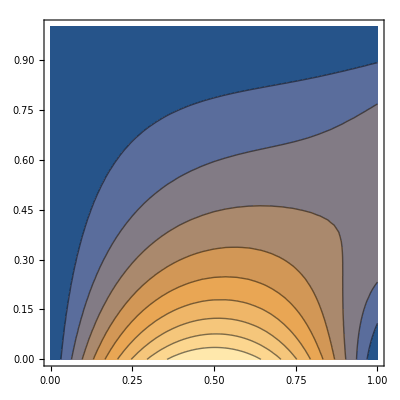

```mathematica
ContourPlot[ϕ[x,y],{x,0,1},{y,0,1}]
```

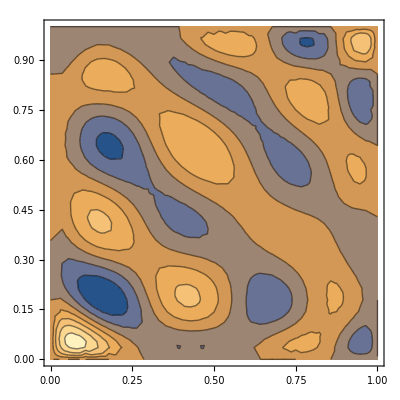

```mathematica
ContourPlot[ϕ[x,y]-ϕex[x,y],{x,0,1},{y,0,1}]
```

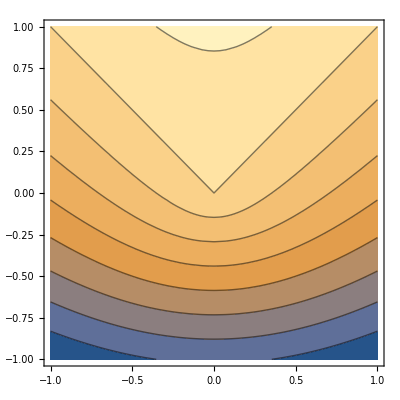

```mathematica
ContourPlot[y-Sqrt[(1-1/2) x^2 + 1/2 y^2],{x,-1,1},{y,-1,1}]
```

```mathematica
Clear["Global`*"]
```